# PreModule

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.002]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 


If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ42]]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.002]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.002]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.002]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6)) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.4,0.6,0.00013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.4,0.6,0.00013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
Print[Ωc1];
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Rbpress[400][[2]]*10^-6
```

760.486

```mathematica
Rbpress[20][[2]]*10^-6
```

501.857

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.4,0.6,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.4,0.6,0.00013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.4,0.6,0.00013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=-(2Pi(210.923*10^6) +2Pi(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

# Figure

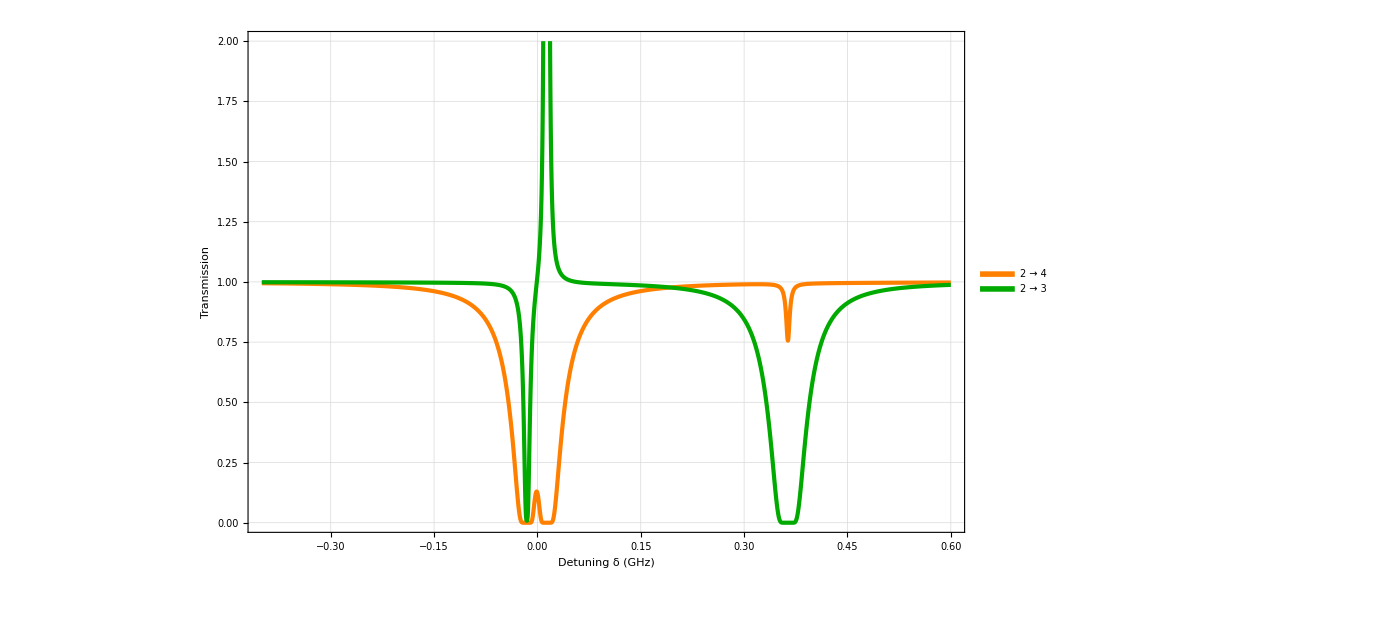

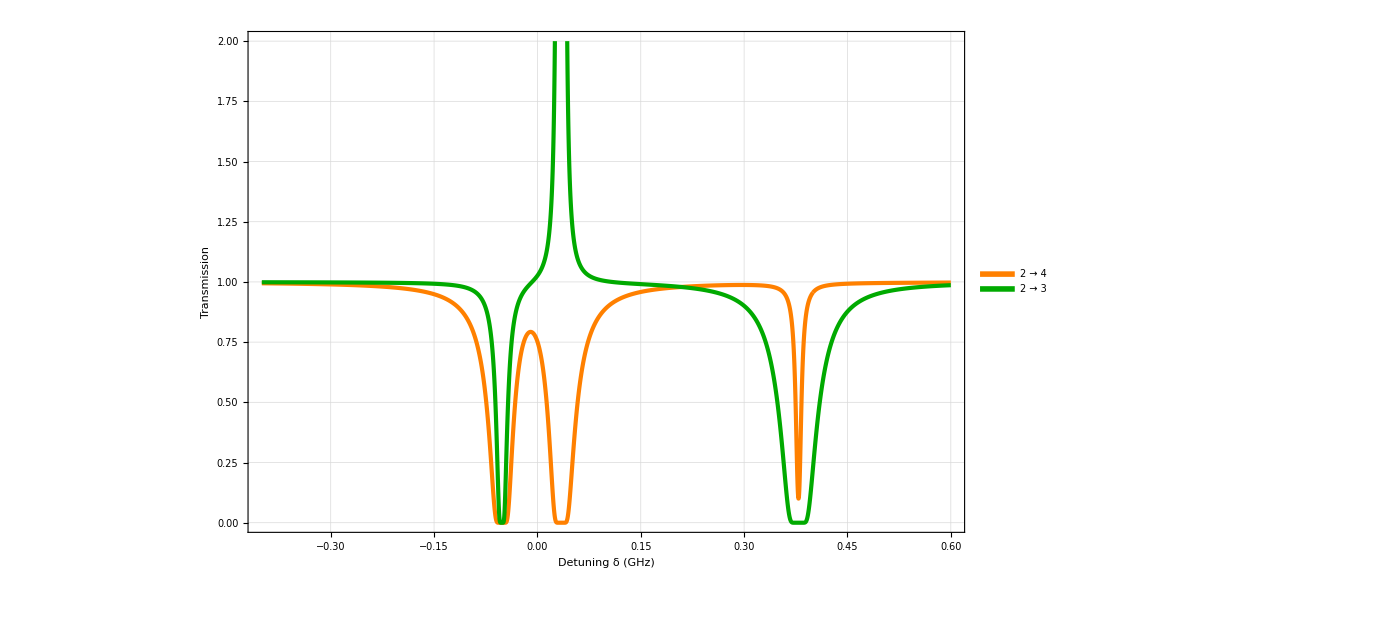

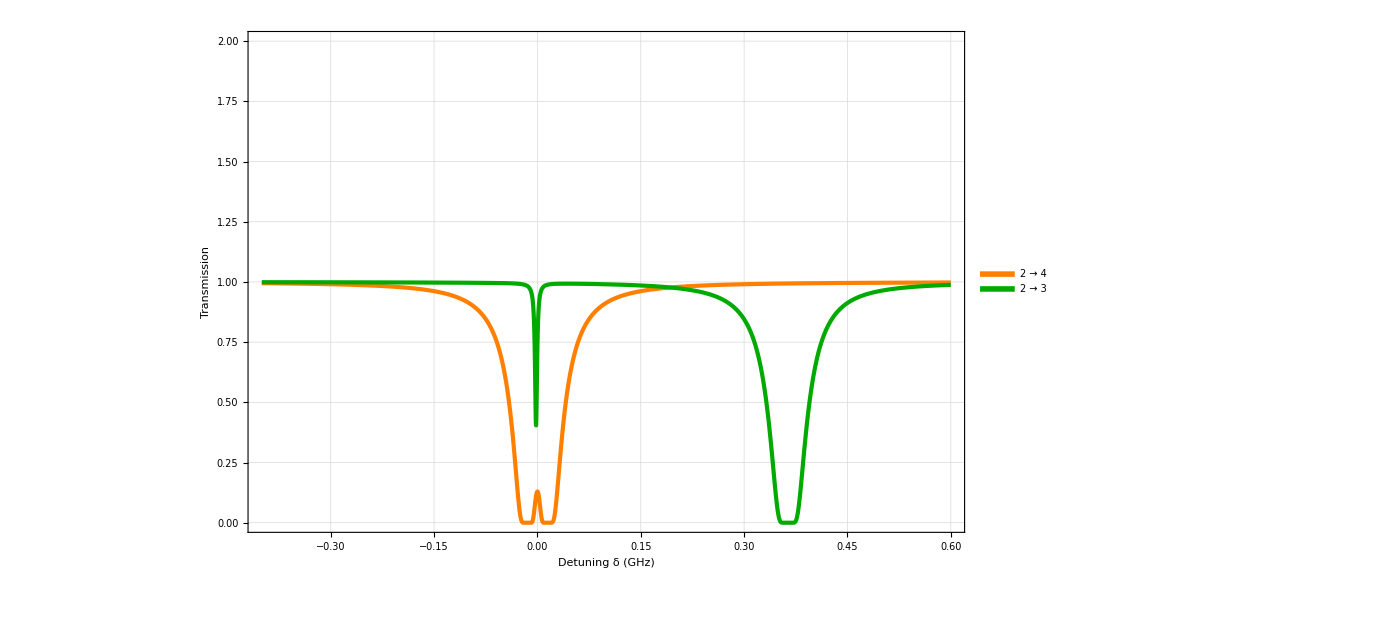

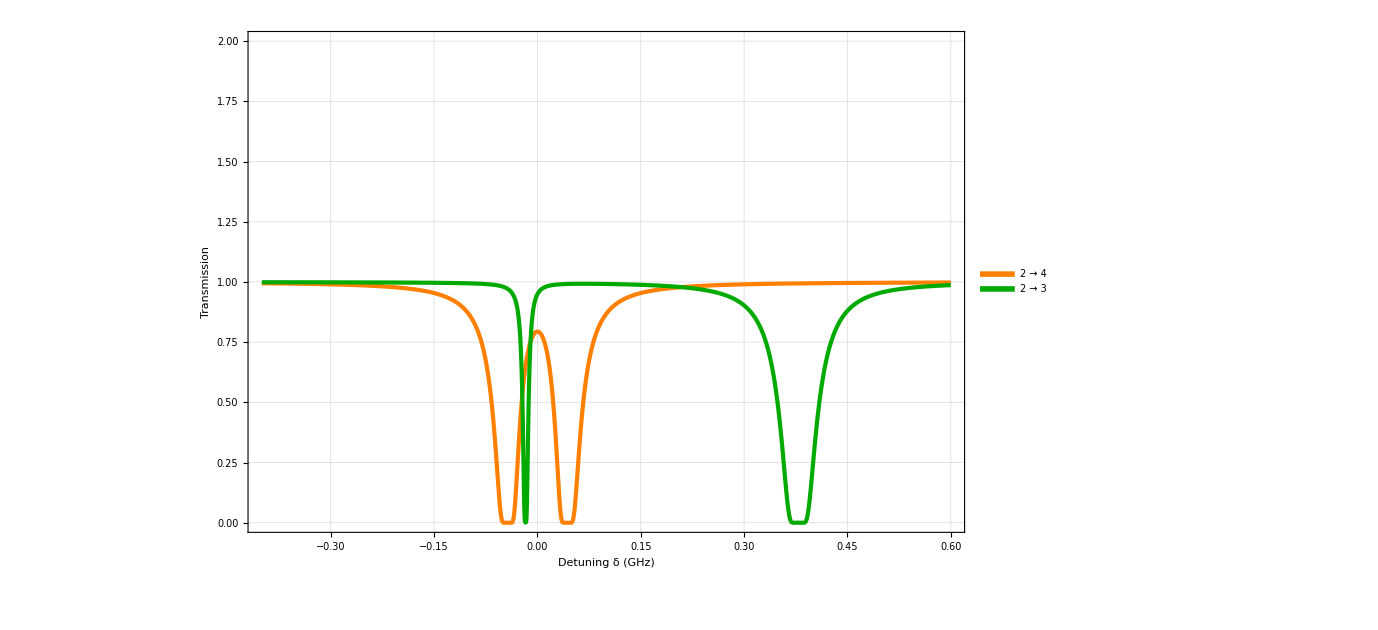

```mathematica
p=15.865;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final4=ListPlot[Lev4Testsc[50,p/1000,1/1000,1.438*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.4,0.6},{0,2}}]
p=142.75;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final5=ListPlot[Lev4Testsc[50,p/1000,1/1000,1.438*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.4,0.6},{0,2}}]
p=15.865;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final6=ListPlot[Lev3Testsc[50,p/1000,1/1000,1.438*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.4,0.6},{0,2}}]
p=142.75;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final7=ListPlot[Lev3Testsc[50,p/1000,1/1000,1.438*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.4,0.6},{0,2}}]
```

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\GoodFigure - Copy"]
Export["Figure2lv4O5g0.25.eps",final4]
Export["Figure2lv4O15g0.25.eps",final5]
Export["Figure2lv3O05g0.25.eps",final6]
Export["Figure2lv3O15g0.25.eps",final7]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\GoodFigure - Copy

Figure2lv4O5g0.25.eps

Figure2lv4O15g0.25.eps

Figure2lv3O05g0.25.eps

Figure2lv3O15g0.25.eps

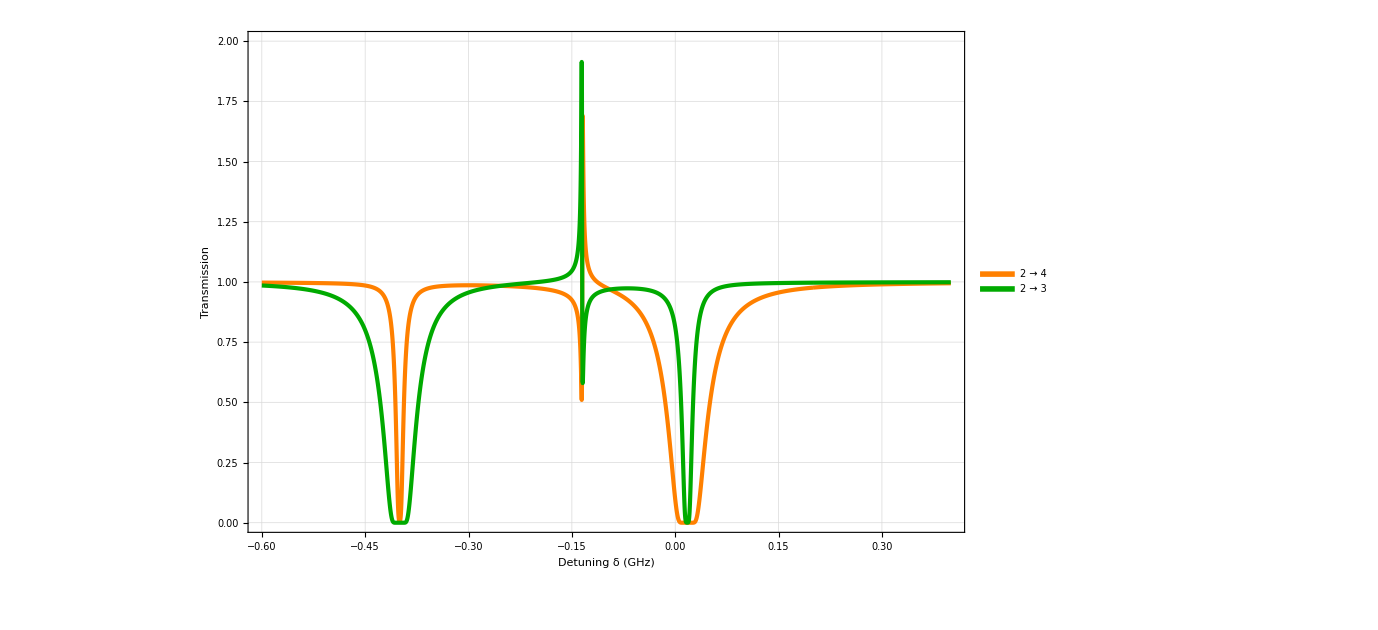

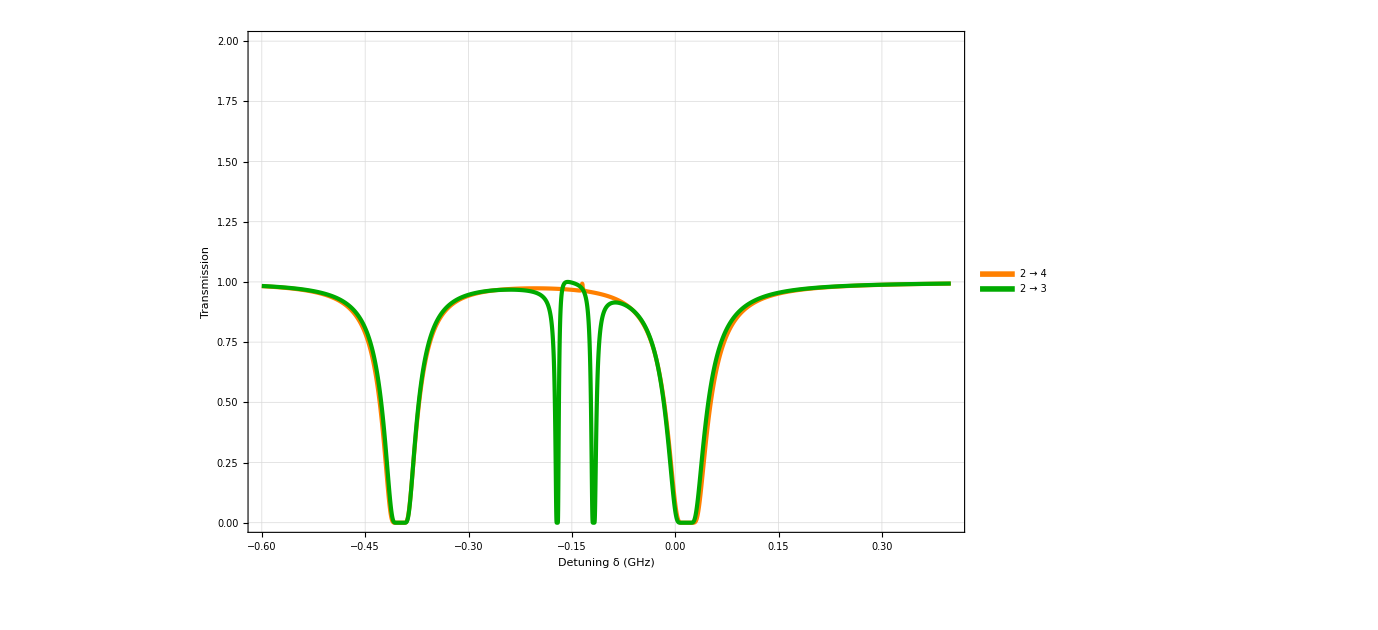

```mathematica
p=200;
δ=-156;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final4=ListPlot[Lev4Testsc[50,p/1000,1/1000,0*10^6,δ*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final41=ListPlot[{Lev4Testsc[50,p/1000,1/1000,0*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
```

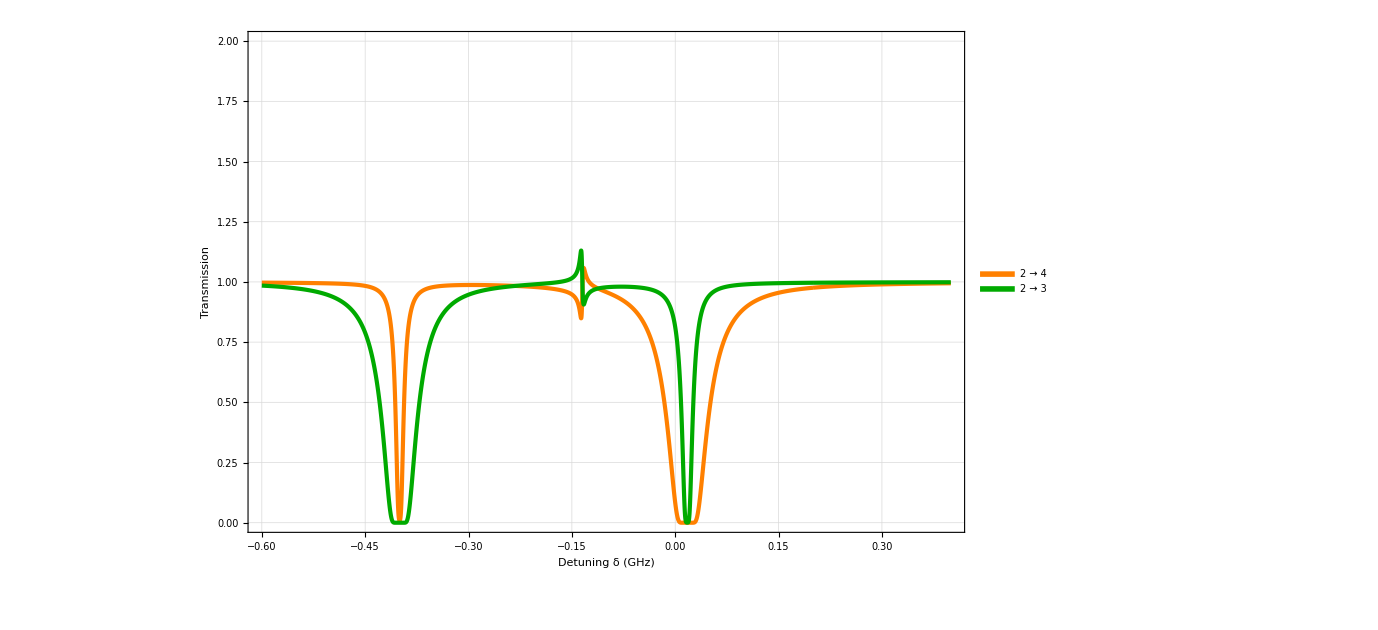

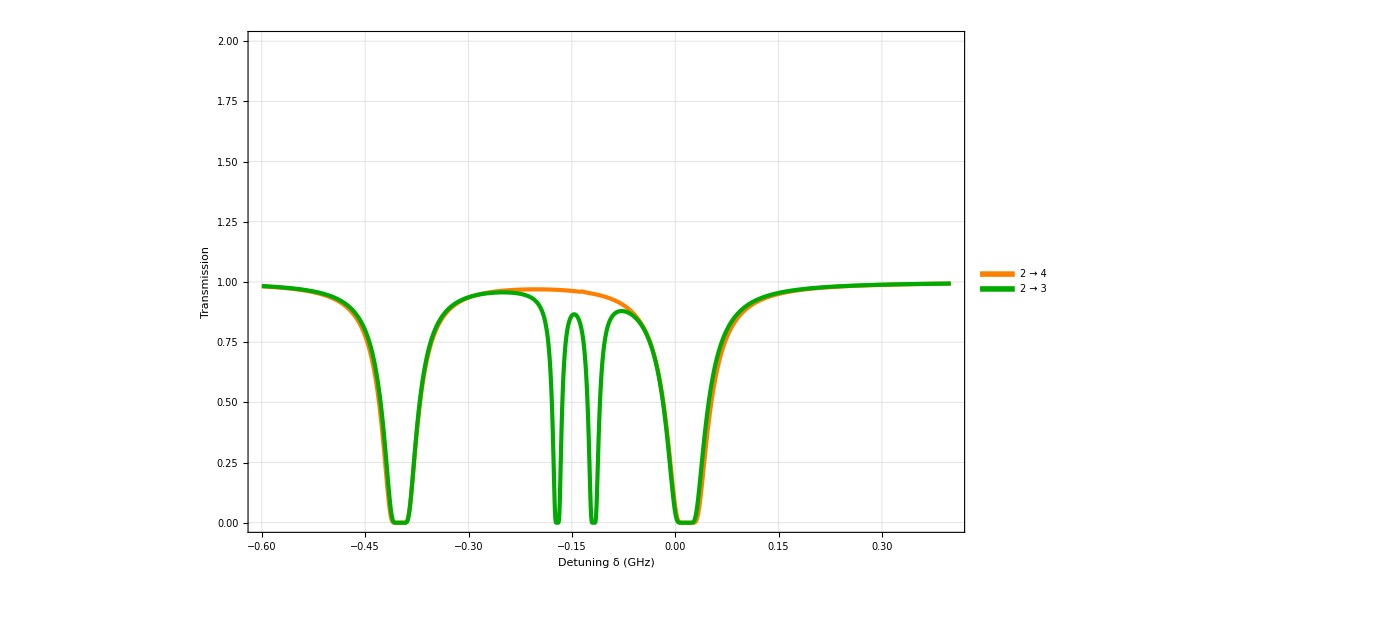

```mathematica
p=200;
δ=-156;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final4=ListPlot[Lev4Testsc[50,p/1000,1/1000,1.5*10^6,δ*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
final4=ListPlot[{Lev4Testsc[50,p/1000,1/1000,1.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,1.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
```

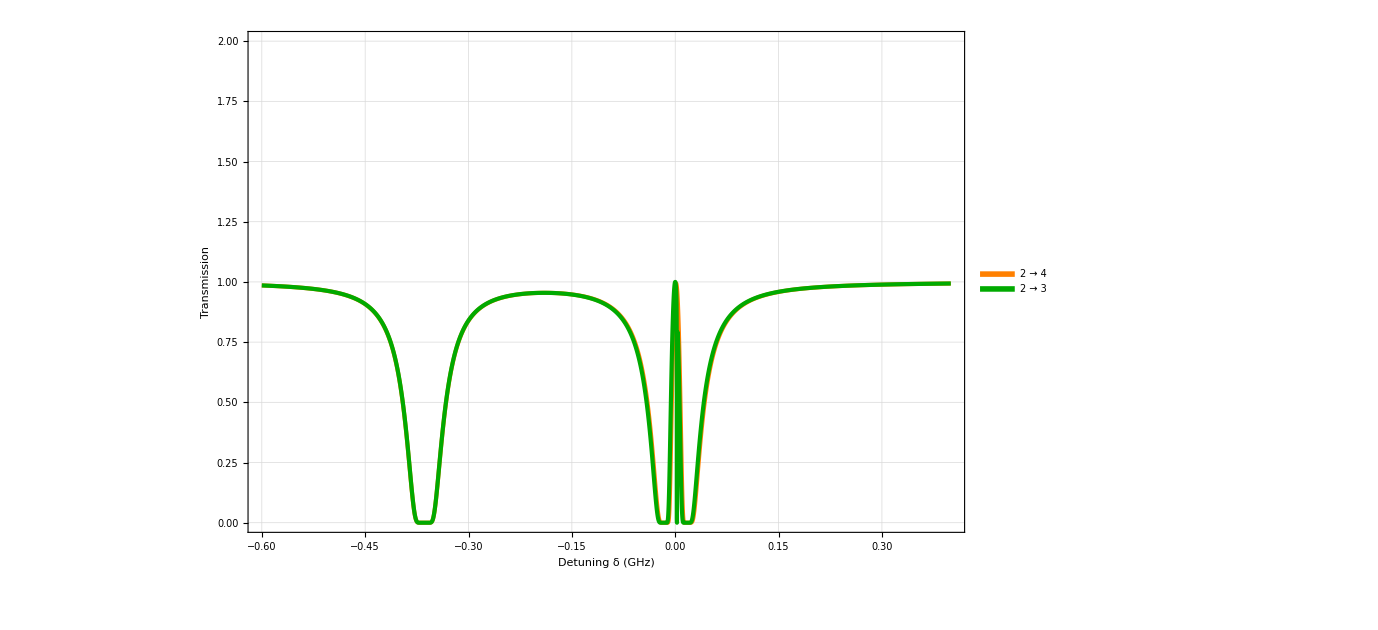

```mathematica
p=20;
δ=0;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final4=ListPlot[{Lev4Testsc[50,p/1000,1/1000,0*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
```

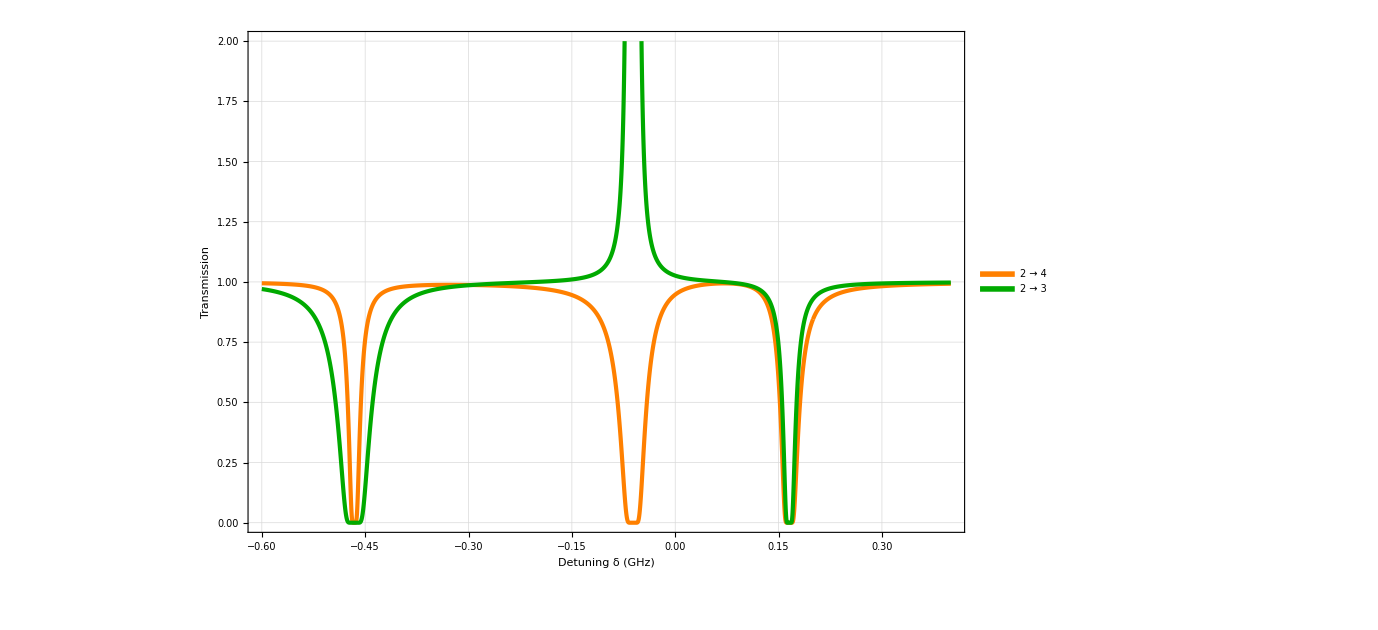

```mathematica
p=1000.865;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final4=ListPlot[Lev4Testsc[50,p/1000,1/1000,0*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
```